```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ=75.8;
ν=-482.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=300;
```

# Mean-field effective potential

## effective potential

92.325526

135.695

480.438

300.058

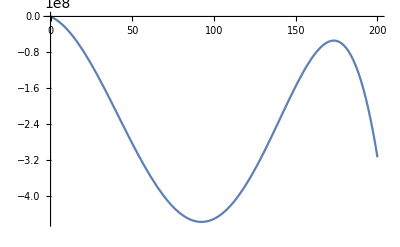

```mathematica
a=FindMinimum[{V[a1^2/2,h,1,0.,λ,ν,c]+Vvacuum[a1^2/2,h,M1],0<a1<195},{a1,90},WorkingPrecision->8][[2]][[1]][[2]]//Quiet

√Vd1rhovacuum[a^2/2,h,λ,ν,M1]
√(Vd1rhovacuum[a^2/2,h,λ,ν,M1]+2*a^2/2*Vd2rhovacuum[a^2/2,h,λ,ν,M1])
√mf2[h,a^2/2]
Plot[{V[a^2/2,h,1,0,λ,ν,c]+Vvacuum[a^2/2,h,M1]},{a,0,200},PlotRange->All]
(*Zps[a^2/2,h,1.,0.,400]*)
```

```mathematica
(*fpi=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,μ,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];*)
```

```mathematica
ListPlot[fpi,PlotRange->All]
```

ListPlot::lpn: fpi 不是由数字或者数对组成的列表.

ListPlot[fpi,PlotRange→All]

# Mean-field wave function renormalization

## threshold functions and equations

```mathematica
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,20000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
```

```mathematica
F2PH[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ])*q^3;
F3PH[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]));
ZpsthrPH[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2PH[q,ρ,h,T,μ]+2/3 F3PH[q,ρ,h,T,μ]),{q,0.,500.,20000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
```

```mathematica
F2CA[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3CA[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(3(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
ZpsthrCA[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2CA[q,ρ,h,T,μ]+2/3 F3CA[q,ρ,h,T,μ]),{q,0.,500.,20000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

## σ data at μ=0

```mathematica
fpimu0=Table[Flatten[ParallelTable[{FindMinimum[{V[a^2/2,h,i*10.,j*0.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,10},AccuracyGoal->5,PrecisionGoal->5][[2]][[1]][[2]]//Quiet},{i,1,200}]],{j,0,0}];
```

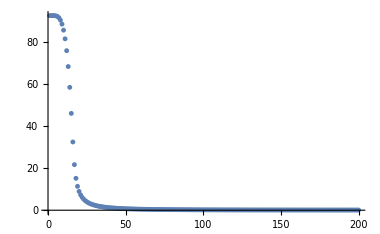

```mathematica
ListPlot[fpimu0,PlotRange->All]
```

```mathematica
Export["./sigma_T_mu0.dat",fpimu0]
```

./sigma_T_mu0.dat

```mathematica
mfdata=Flatten[√mf2[6.5,fpimu0^2/2]];
```

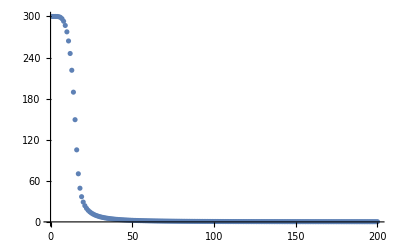

```mathematica
ListPlot[mfdata,PlotRange->All]
```

```mathematica
Tdata=Table[i*10,{i,1,200}]
```

{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000,1010,1020,1030,1040,1050,1060,1070,1080,1090,1100,1110,1120,1130,1140,1150,1160,1170,1180,1190,1200,1210,1220,1230,1240,1250,1260,1270,1280,1290,1300,1310,1320,1330,1340,1350,1360,1370,1380,1390,1400,1410,1420,1430,1440,1450,1460,1470,1480,1490,1500,1510,1520,1530,1540,1550,1560,1570,1580,1590,1600,1610,1620,1630,1640,1650,1660,1670,1680,1690,1700,1710,1720,1730,1740,1750,1760,1770,1780,1790,1800,1810,1820,1830,1840,1850,1860,1870,1880,1890,1900,1910,1920,1930,1940,1950,1960,1970,1980,1990,2000}

```mathematica
ZhighT=-(2 h^2 Nc)/(4π)^2 Log[Tdata/300];
```

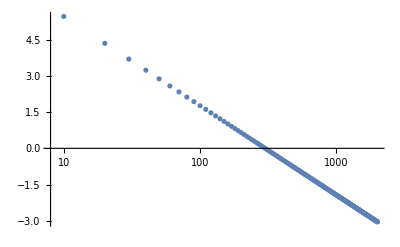

```mathematica
ListPlot[Transpose[{Tdata,ZhighT}],ScalingFunctions->{"Log",Automatic}]
```

```mathematica
Export["ZhighTdata.dat",ZhighT];
```

## σ data at μ=320

```mathematica
fpimu320=Table[Flatten[ParallelTable[{FindMinimum[{V[a^2/2,h,i*10.,320.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,10},AccuracyGoal->5,PrecisionGoal->5][[2]][[1]][[2]]//Quiet},{i,1,200}]],{j,0,0}];
```

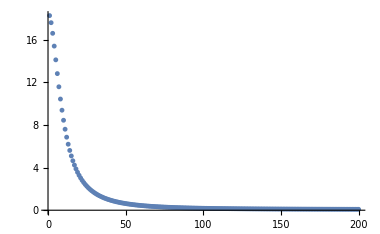

```mathematica
ListPlot[fpimu320,PlotRange->All]
```

```mathematica
mfdata=Flatten[√mf2[6.5,fpimu320^2/2]];
```

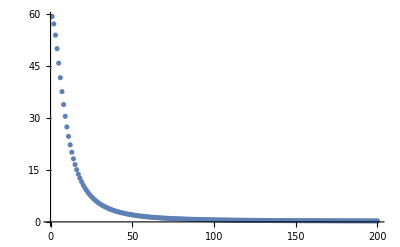

```mathematica
ListPlot[mfdata,PlotRange->All]
```

```mathematica
Tdata=Table[i*10,{i,1,200}]
```

{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000,1010,1020,1030,1040,1050,1060,1070,1080,1090,1100,1110,1120,1130,1140,1150,1160,1170,1180,1190,1200,1210,1220,1230,1240,1250,1260,1270,1280,1290,1300,1310,1320,1330,1340,1350,1360,1370,1380,1390,1400,1410,1420,1430,1440,1450,1460,1470,1480,1490,1500,1510,1520,1530,1540,1550,1560,1570,1580,1590,1600,1610,1620,1630,1640,1650,1660,1670,1680,1690,1700,1710,1720,1730,1740,1750,1760,1770,1780,1790,1800,1810,1820,1830,1840,1850,1860,1870,1880,1890,1900,1910,1920,1930,1940,1950,1960,1970,1980,1990,2000}

```mathematica
ZhighT=-(2 h^2 Nc)/(4π)^2 Log[Tdata/300];
```

```mathematica
ListPlot[Transpose[{Tdata,ZhighT}],ScalingFunctions->{"Log",Automatic}]
```

-Graphics-

```mathematica
Export["ZhighTdata.dat",ZhighT];
```

## Z_π(p=0)

### μ=0

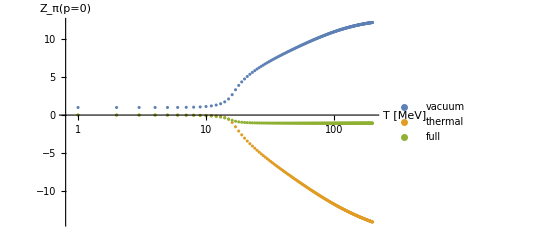

```mathematica
Zpsvac1[ρ_,h_,M_]:=Zpsvac[ρ,h,M]+1.;
ZpsthrCA[ρ_,h_,T_,μ_,M_]:=ZpsthrCA[ρ,h,T,μ];
ZpsthrPH[ρ_,h_,T_,μ_,M_]:=ZpsthrPH[ρ,h,T,μ];
(*Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;*)
Zvac=Flatten[ParallelTable[{Zpsvac1[(fpimu0[[1]][[i]])^2/2,h,300.]//Quiet},{i,1,200}],1];
(*Zvac2=Flatten[ParallelTable[Zpsvac1[(fpimu0[[1]][[l]])^2/2,h,N[i],0.,300.]//Quiet,{i,1500,10000}]];*)
ZthrCA=Flatten[ParallelTable[{ZpsthrCA[(fpimu0[[1]][[i]])^2/2,h,N[10i],0.,300.]//Quiet},{i,1,200}],1];
ZthrPH=Flatten[ParallelTable[{ZpsthrPH[(fpimu0[[1]][[i]])^2/2,h,N[10i],0.,300.]//Quiet},{i,1,200}],1];
(*Zall=Flatten[ParallelTable[{i,Zps[(fpimu0[[1]][[i]])^2/2,h,N[i],0.,300.]//Quiet},{i,1,1500}],0];
Zall2=Flatten[ParallelTable[{i,Zps[(fpimu0[[1]][[l]])^2/2,h,N[i],0.,300.]//Quiet},{i,1500,10000}],0];*)
(*Λ=10000.;
l=Length[fpimu0[[1]]];*)
ZplotM300=ListPlot[{Zvac,ZthrCA,ZthrPH},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,All},PlotLegends->{"vacuum","thermal","full"},ScalingFunctions->{"Log",Automatic}]
```

```mathematica
Export["./Zvac.dat",Zvac];
Export["./ZCA.dat",ZthrCA];
Export["./ZPH.dat",ZthrPH];
```

### μ=320

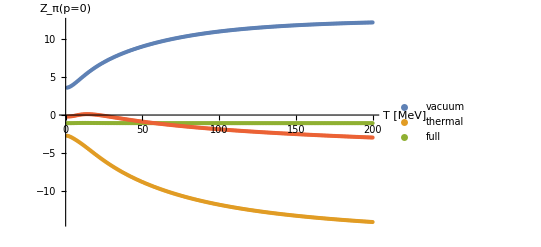

```mathematica
Zpsvac1[ρ_,h_,M_]:=Zpsvac[ρ,h,M]+1.;
ZpsthrCA[ρ_,h_,T_,μ_,M_]:=ZpsthrCA[ρ,h,T,μ];
ZpsthrPH[ρ_,h_,T_,μ_,M_]:=ZpsthrPH[ρ,h,T,μ];
Zvacmu320=Flatten[ParallelTable[{Zpsvac1[(fpimu320[[1]][[i]])^2/2,h,300.]//Quiet},{i,1,200}],1];
ZthrCAmu320=Flatten[ParallelTable[{ZpsthrCA[(fpimu320[[1]][[i]])^2/2,h,N[10i],320.,300.]//Quiet},{i,1,200}],1];
ZthrPHmu320=Flatten[ParallelTable[{ZpsthrPH[(fpimu320[[1]][[i]])^2/2,h,N[10i],320.,300.]//Quiet},{i,1,200}],1];
Zplot320=ListPlot[{Zvacmu320,ZthrCAmu320,ZthrPHmu320,Zvac320+ZthrCAmu320+ZthrPHmu320},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,All},PlotLegends->{"vacuum","thermal","full"},ScalingFunctions->{Automatic,Automatic}]
```

```mathematica
Export["./Zvacmu320.dat",Zvacmu320];
Export["./ZCAmu320.dat",ZthrCAmu320];
Export["./ZPHmu320.dat",ZthrPHmu320];
```